```mathematica
(* m is the mass of ϕ, M is the mass of N *)
α[s_, m_, M_]:=m^2-M^2-1/2 s;
β[s_,m_,M_]:=(s(s/4-m^2))^(1/2);
```

```mathematica
σ[s_,m_,M_,g_]:=(g^4 M^2)/(128 π)((s-4 m^2)/s)^(1/2)(4/(α[s, m, M]^2-β[s,m,M]^2) + 2/(α[s,m,M] β[s,m,M])Log[(α[s,m,M]+β[s,m,M])/(α[s,m,M]-β[s,m,M])]);
```

```mathematica
Σ[s_,m_,M_,g_]:=(g^4 M^2)/(32 π)(((s/4-m^2)/s)^(1/2)  2/((m^2-M^2-s/2)^2-s(s/4-m^2))+1/(s(m^2-M^2-s/2))Log[(m^2-M^2-s/2+(s(s/4-m^2))^(1/2))/(m^2-M^2-s/2-(s(s/4-m^2))^(1/2))]);
```

7.07107

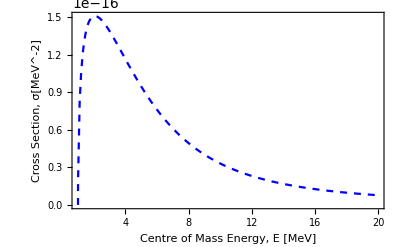

1.02775×10^6

```mathematica
eV   =1 10^-6;
MeV=10^6 10^-6;
PeV=10^15 10^-6;
pc  = 3.0857 * 10^18;
Gpc = 10^9 pc;
g=10^-3;
Subscript[m, ν]=0.1eV;
Subscript[m, ϕ]=1MeV;
Subscript[m, N]=10MeV;
Subscript[E, ν] = 1 PeV;
Subscript[E, c]= (1/2(Subscript[E, ν] Subscript[m, ν] + Subscript[m, ν]^2))^(1/2)
Subscript[n, ν]=340; (*cm^-3*)
(* 1 eV = 8065.54429 cm^-1 *)
conv = 8065.54429 10^6;

Plot[σ[4 x^2,Subscript[m, ϕ],Subscript[m, N],g],{x,0, 20 Subscript[m, ϕ]},GridLines->{{{Subscript[m, ϕ],{Black,Dotted}}, {Subscript[E, c], {Thick,Red}}}}, PlotPoints->200, MaxRecursion->15, 
PlotStyle->{{Blue, Dashed}}, PlotTheme->"Scientific",FrameLabel->{{RawBoxes[RowBox[{RowBox[{"Cross"," ","Section"}],","," ","σ[MeV^-2]"}]],None},{RawBoxes[RowBox[{RowBox[{"Centre"," ","of"," ","Mass"," ","Energy"}],","," ","E", " ", "[MeV]"}]],None}},PlotLabel->None,LabelStyle->{8,GrayLevel[0]}, PlotRange->All]
Subscript[σ, pev] = σ[(2 Subscript[E, c])^2,Subscript[m, ϕ],Subscript[m, N],g];
l=(conv^2)/(Subscript[n, ν] Subscript[σ, pev]); 
l / Gpc
Subscript[d, b]=1.75 Gpc;
```